```mathematica
NormalizedData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
```

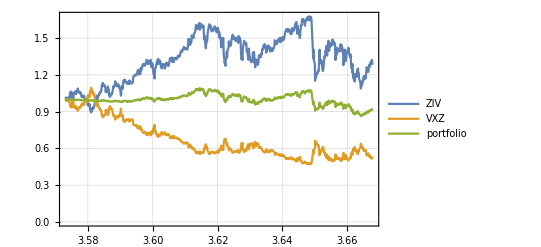

```mathematica
start=DatePlus[Today,-Quantity[3,"Years"]];
end=Today;
ziv=NormalizedData["ZIV",start,end];
vxz=NormalizedData["VXZ",start,end];
mean=Transpose@{ziv[[All,1]],Mean/@Transpose@{ziv[[All,2]],vxz[[All,2]]}};
DateListPlot[{ziv,vxz,mean},PlotLegends->{"ZIV","VXZ","portfolio"},PlotTheme->"Detailed"]
```

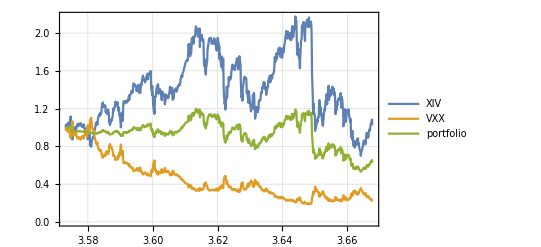

```mathematica
xiv=NormalizedData["XIV",start,end];
vxx=NormalizedData["VXX",start,end];
mean=Transpose@{xiv[[All,1]],Mean/@Transpose@{xiv[[All,2]],vxx[[All,2]]}};
DateListPlot[{xiv,vxx,mean},PlotLegends->{"XIV","VXX","portfolio"},PlotTheme->"Detailed"]
```

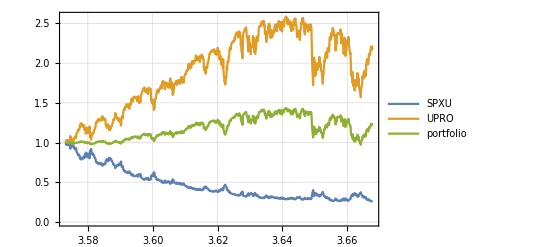

```mathematica
spxu=NormalizedData["SPXU",start,end];
upro=NormalizedData["UPRO",start,end];
mean=Transpose@{spxu[[All,1]],Mean/@Transpose@{spxu[[All,2]],upro[[All,2]]}};
DateListPlot[{spxu,upro,mean},PlotLegends->{"SPXU","UPRO","portfolio"},PlotTheme->"Detailed"]
```

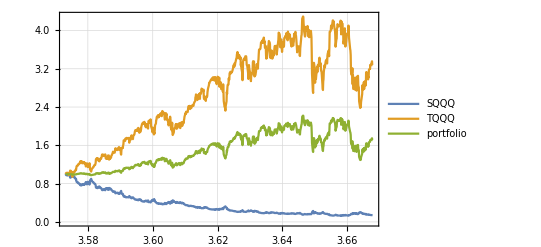

```mathematica
sqqq=NormalizedData["SQQQ",start,end];
tqqq=NormalizedData["TQQQ",start,end];
mean=Transpose@{sqqq[[All,1]],Mean/@Transpose@{sqqq[[All,2]],tqqq[[All,2]]}};
DateListPlot[{sqqq,tqqq,mean},PlotLegends->{"SQQQ","TQQQ","portfolio"},PlotTheme->"Detailed"]
```

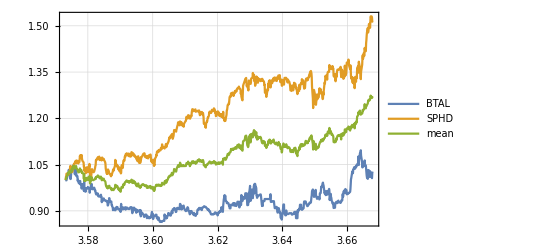

```mathematica
btal=NormalizedData["BTAL",start,end];
invalid=First@FirstPosition[btal[[All,1]],_?(#=={2015,4,29}&)];
btal=Delete[btal,invalid];
sphd=NormalizedData["SPHD",start,end]//Delete[#,invalid]&;
mean=Transpose@{btal[[All,1]],Mean/@Transpose@{btal[[All,2]],sphd[[All,2]]}};
DateListPlot[{btal,sphd,mean},PlotLegends->{"BTAL","SPHD","mean"},PlotTheme->"Detailed"]
```

```mathematica
NormalizedData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
PortfolioChart[stock_,inverse_,start_,end_]:=Module[{btal,invalid,s1,s2,portfolio,portfolio2,chart},
btal=NormalizedData["BTAL",start,end];
invalid=First@FirstPosition[btal[[All,1]],_?(#=={2015,4,29}&)];
btal=Delete[btal,invalid];
s1=NormalizedData[stock,start,end]//Delete[#,invalid]&;
s2=NormalizedData[inverse,start,end]//Delete[#,invalid]&;
portfolio=Transpose@{s1[[All,1]],Mean/@Transpose@{btal[[All,2]],s1[[All,2]]}};
portfolio2=Transpose@{s1[[All,1]],Mean/@Transpose@{s2[[All,2]],s1[[All,2]]}};
chart=DateListPlot[{btal,s1,s2,portfolio,portfolio2},PlotLegends->{"BTAL",stock,inverse,"BTAL & "<>stock,inverse<>" & "<>stock},PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20}]
]
```

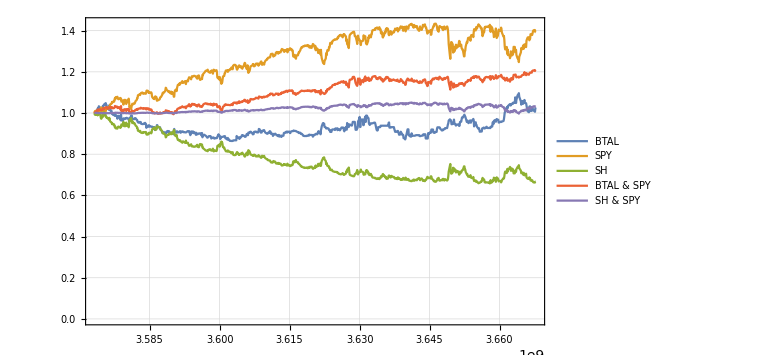

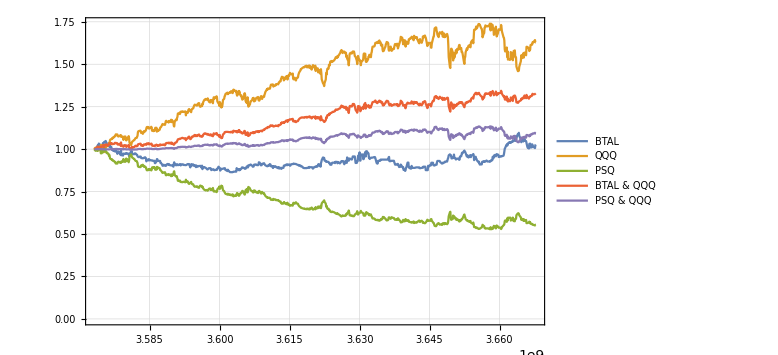

```mathematica
start=DatePlus[Today,-Quantity[3,"Years"]];
chart1=PortfolioChart["SPY","SH",start,Today]
chart2=PortfolioChart["QQQ","PSQ",start,Today]
```

```mathematica
Export[NotebookDirectory[]<>"chart1.png",Magnify@chart1];
Export[NotebookDirectory[]<>"chart2.png",Magnify@chart2];
```